## Week 2 – Stanford Machine Learning

### Multivariate Regression via Gradient Descent

Let us create some random data, say housing size, number of bedrooms, and age of the house as a feature matrix, and price levels on y. Although we deal with a multi-dimensional case, traditionally we consider the training features as a part of x and the training labels as a part of y.

```mathematica
trainX={{100,320,213,512,58,84,113}, {1,4,2,4,0,1,1},{7,4,12,21,9,3,31}};
trainY={140000,400000,241000,489000,78000,123000,139000};
grid=Grid[MapThread[Prepend,{Prepend[Transpose@Append[trainX,trainY],{"Size (feet^2)","Bedrooms","Age (years)","Price ($)"}],Join[{"Example"},Range[1,7]]}],Dividers->Center]
```

Example | Size (feet^2) | Bedrooms | Age (years) | Price ($)
1 | 100 | 1 | 7 | 140000
2 | 320 | 4 | 4 | 400000
3 | 213 | 2 | 12 | 241000
4 | 512 | 4 | 21 | 489000
5 | 58 | 0 | 9 | 78000
6 | 84 | 1 | 3 | 123000
7 | 113 | 1 | 31 | 139000

In order to make this data work better with our gradient descent algorithm, we scale all the features through mean normalisation and by dividing by the standard deviation.

```mathematica
trainXScaled=(trainX-Mean[Transpose@trainX])/StandardDeviation[Transpose@trainX];
```

We could also have used the range of the list as below, but the standard deviation works just as well.

```mathematica
trainXScaledWithRange=(trainX-Mean[Transpose@trainX])/(Max[#]-Min[#]&/@trainX);
```

Now, we define a our hypothesis function which is the dot product between any two n-dimensional vectors

```mathematica
Hyp[v_,x_]:=Dot[v,x]
```

Then, before defining the cost function, we modify the training data a final time to include the constant in our multivariate model, usually x_0. That is, we prepend a column of ones.

```mathematica
trainXFinal = Join[{Table[1,{Length[trainY]}]},trainXScaled];
```

The cost function is defined below as follows.

```mathematica
Cost[v_]:=1/(2Length[trainXFinal])Total[Apply[Hyp,{v,#1}&/@Transpose@trainXFinal,{1}]^2-trainY];
```

We then create the step function and assign the learning rate.

```mathematica
α=0.03;
Step[v_]:=
v-α Grad[Cost[{w,x,y,z}],{w,x,y,z}]/.{w->v[[1]],x->v[[2]],y->v[[3]],z->v[[4]]}
```

To check that the step function works, we can plot the step function as a function of the iteration number to picture the learning rate. We do so by creating the learning function

```mathematica
Learning[x_]:=Cost@Nest[Step,{1,1,1,1},x];
```

As seen below, we learn, and so our gradient descent algorithm for multiple variables works.

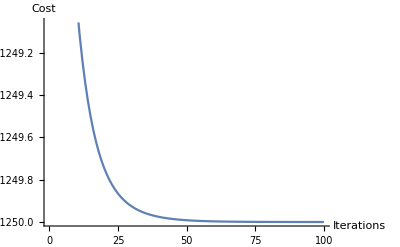

```mathematica
learningRate=ListLinePlot[#,AxesLabel->{"Iterations","Cost"}]&@Transpose@{Range[0,100],Learning/@Range[0,100]}
```

Thus, we can predict the new housing prices as follows

```mathematica
optimalParameters=Nest[Step,{1,1,1,1},10000]Join[{1}, StandardDeviation[Transpose@trainX]]+Join[{1},Mean[Transpose@trainX]];
Model=Manipulate[Hyp[{1,size,bedrooms,age},optimalParameters],{size,10,1000},{bedrooms,0,10},{age,0,70}]
```

As seen, our model computes the predicted housing price in a very poor manner compared to the sample cases. The reason for this is two-fold; firstly, our data set is not large enough for the model to correctly capture the fact that age is a negative attribute. Moreover, we did a linear fit, which probably wasn’t the best possible model.

### Polynomial Regression

Using the dataset from week1, we will try and fit a polynomial model instead. First, we insert and plot the data.

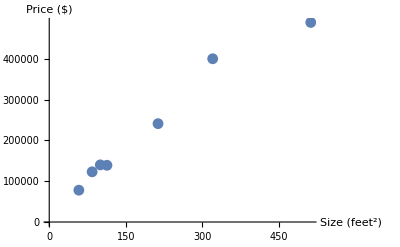

```mathematica
trainX={100,320,213,512,58,84,113};
trainY={140000,400000,241000,489000,78000,123000,139000};
reglp=ListPlot[Transpose@{trainX,trainY},AxesLabel->{"Size (feet^2)","Price ($)"}];
Show[reglp]
```

We then define a hypothesis and a cost function. Note that, this time, we add an extra parameter for the squared term.

```mathematica
Hyp[v_,x_]:=v[[1]]+v[[2]] x+v[[3]] x^2;
Cost[v1_,v2_,v3_]:=1/(2Length[trainX])Total[(Hyp[{v1,v2,v3},#1]-#2)^2&@@@Transpose@{trainX,trainY}];
```

We create the step function; again note the very low learning rates, which could have been avoided by normalising the data as above.

```mathematica
αv1=0.1;
αv2 =0.00001;
αv3=0.0000000001;
Step[v1_,v2_,v3_]:=
{v1-αv1 D[Cost[x,y,z],x]/.{x->v1,y->v2,z->v3},v2-αv2 D[Cost[x,y,z],y]/.{x->v1,y->v2,z->v3},v3-αv3 D[Cost[x,y,z],z]/.{x->v1,y->v2,z->v3}};
```

We check that it works via the learning rate plot

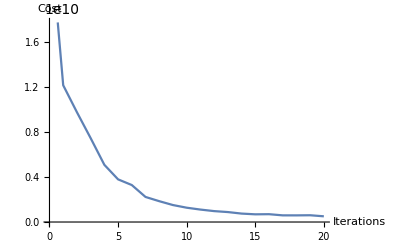

```mathematica
Learning[x_]:=Cost@@Nest[Apply[Step,#]&,{RandomReal[],RandomReal[],RandomReal[]},x];
learningRate=ListLinePlot[#,AxesLabel->{"Iterations","Cost"}]&@Transpose@{Range[0,20],Learning/@Range[0,20]}
```

And then step through the algorithm ten times, to plot all intermediate steps.

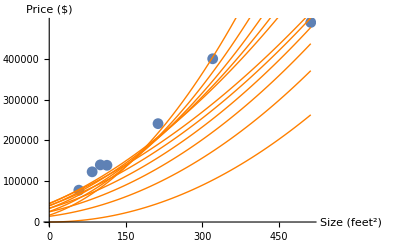

```mathematica
gd=NestList[Apply[Step,#]&,{1,1,1},10];
gdpp=Show[Plot[Hyp[#1,x],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}]&/@gd];
Show[gdlp,gdpp]
```

As seen, we do a very poorly fit over the first 10 iterations. However, if we plot the parameters after higher iterations as seen below, then the fit becomes better.

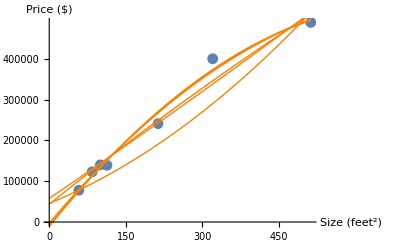

```mathematica
gdit=Nest[Apply[Step,#]&,{1,1,1},#]&/@{10,50,100,500,1000,5000,10000};
gdpp=Show[Plot[Hyp[#1,x],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}]&/@gdit];
Show[gdlp,gdpp]
```

### Normal Equation

As seen, our gradient descent algorithm took long time in order for us to actually derive at a useful answer. We could have optimised it by scaling the features and readjusting the weights. However, another method to get the precise parameters for the lowest cost, is the normal equation.

We reuse the same data from the beginning.

```mathematica
trainX={Table[1,{7}],{100,319,215,511,57,83,123}, {1,4,2,4,0,1,1},{7,4,12,23,7,3,33}};
trainY={140000,400000,241000,489000,78000,123000,139000};
grid=Grid[MapThread[Prepend,{Prepend[Transpose@Append[trainX,trainY],{"x_0","Size (feet^2)","Bedrooms","Age (years)","Price ($)"}],Join[{"Example"},Range[1,7]]}],Dividers->Center]
```

Example | x_0 | Size (feet^2) | Bedrooms | Age (years) | Price ($)
1 | 1 | 100 | 1 | 7 | 140000
2 | 1 | 319 | 4 | 4 | 400000
3 | 1 | 215 | 2 | 12 | 241000
4 | 1 | 511 | 4 | 23 | 489000
5 | 1 | 57 | 0 | 7 | 78000
6 | 1 | 83 | 1 | 3 | 123000
7 | 1 | 123 | 1 | 33 | 139000

We then compute the precise values through the normal equation, assuming that the matrix is singular. Note that we apply the transposes differently, due to the way mathematica stores matrices.

```mathematica
theta=Inverse[trainX.Transpose[trainX]].trainX.trainY//N
```

{43178.9,545.952,44973.9,-512.509}

Using these parameters in our hypothesis function

```mathematica
Hyp[v_,x_]:=Dot[v,x]
```

we get  much better housing price predictions as seen below. Note that age counts negatively, while bedrooms and size count positively towards the price. This also suggest that we might have done something wrong with the gradient descent algorithm.

```mathematica
Model=Manipulate[Hyp[{1,size,bedrooms,age},{43178.87263686469,545.9516325435968,44973.94772235059,-512.5092974156712}],{size,10,1000},{bedrooms,0,10,1},{age,0,70,1}]
```